```mathematica
Needs["DifferentialEquations`NDSolveUtilities`"];
Needs["HierarchicalClustering`"]
```

### For a wave energy conversion device (modeled as a mass with a linear spring) connected to the FPUT chain

The Hamiltonian for the FPUT Chain is calculated

The Hamiltonian for the device (mass-spring) is calculated

The difference in the Hamiltonians (total energies) is found.  This is the energy that is converted by the device

At the moment, no damping has been applied to the FPU model or the wave energy device

## FPUT model

```mathematica
m=1.;α=0.25;n=32;tf=30000;p=2;b=0.0;a=1;
```

```mathematica
(*ic=Exp[-i^2];*)
ic = a Sin[π i/(n+1)];
(*ic = a Sin[π i n/(n+1)];*)
```

Numerical solution uses the LSODA stiff solver

```mathematica
nsol=NDSolveValue[Flatten[{Table[m x[i]''[t]==(x[i + 1][t] - 2*x[i][t] + x[i - 1][t])(1+ α*(x[i + 1][t] - x[i-1][t]))-b x[i]'[t],{i,n}]/.{x[0][t]:>0,x[n+1][t]:>0},Table[{x[i][0]==ic,x[i]'[0]==0.1},{i,n}]}],Table[x[i],{i,n}],{t,0,tf},MaxSteps->600000,Method->"LSODA"];
```

#### Position

```mathematica
Animate[
ListLinePlot[
Table[
nsol[[j]][time],{j,1,n}
],Mesh->All,PlotRange->{All,{-2,2}},PlotStyle->{Black,Thin},
Frame->True, FrameLabel->{"Mass", "Position"},FrameStyle->Black,BaseStyle->{FontSize->14}
],{time,0,tf,0.5},AnimationRate->70]//Inactivate;
```

```mathematica
Manipulate[
ListLinePlot[
Table[
nsol[[j]][tt],{j,1,n}
],Mesh->All,PlotRange->{All,{-2,2}},PlotStyle->{Black,Thin},
Frame->True, FrameLabel->{"Mass", "Position"},FrameStyle->Black,BaseStyle->{FontSize->14}
],{tt,0,tf,10}]
```

InterpolatingFunction::dmval: Input value {60000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Animate[
ListLinePlot[
Table[
nsol[[j]][tt]-nsol[[j-1]][tt],{j,2,n}
],Mesh->All,PlotRange->{All,{-1,1}},PlotStyle->{Black,Thin},
Frame->True, FrameLabel->{"Mass", "Position"},FrameStyle->Black,BaseStyle->{FontSize->14}
],{tt,0,tf,0.5},AnimationRate->14]//Inactivate;
```

#### Velocity and Momentum calculation for FPUT

Since NDSolveValue was used, the velocity can be easily calculated using prime notation, viz., velocity = nsol[[j]]’[t]

Here, j is the particle number and t is the current time.

An animation of velocity is below.

Velocity

```mathematica
Animate[
ListLinePlot[
Table[
nsol[[j]]'[tt],{j,1,n}
],Mesh->All,PlotRange->{All,{-1,1}},PlotStyle->{Black,Thin},
Frame->True, FrameLabel->{"Mass", "Velocity"},FrameStyle->Black,BaseStyle->{FontSize->14}
],{tt,0,tf,0.5},AnimationRate->10]//Inactivate;
```

Hamiltonian

The Hamiltonian (with the nonlinear term in the FPUT) as given in Weissert equation 1.4, page 19:  0.5( (nsol[[j]][tt])^2+(nsol[[j]]'[tt]-nsol[[j-1]]'[tt])^2 
)+ (α/3)(nsol[[j]]'[tt]-nsol[[j-1]]'[tt])^3

```mathematica
Animate[
ListLinePlot[
Table[
0.5(
(nsol[[j]][tt])^2+(nsol[[j]]'[tt]-nsol[[j-1]]'[tt])^2 
)+ (α/3)(nsol[[j]]'[tt]-nsol[[j-1]]'[tt])^3,{j,2,n}
],Mesh->All,PlotRange->{All,{0,1.75}},PlotStyle->{Black,Thin},
Frame->True, FrameLabel->{"Mass", "Velocity"},FrameStyle->Black,BaseStyle->{FontSize->14}
],{tt,0,tf,0.5},AnimationRate->10]//Inactivate;
```

## Wave energy device (WED) (mass with linear spring)

Numerical solution

InterpolatingFunction[{{0., 30000.}}, <>]

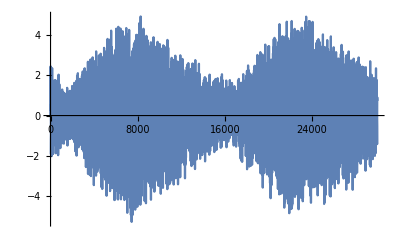

```mathematica
m=1.; k=1.; 
wsol =NDSolveValue[{
m x''[t]+k x[t] ==0,
x[0]==0.,x'[0]==0.0001},
x,{t,0,tf}]//Inactivate;
wsol =NDSolveValue[{
m x''[t]+k (x[t]-nsol[[20]][t]) ==0,
x[0]==0.,x'[0]==0.0001},
x,{t,0,tf}]
Plot[wsol[t],{t,0,tf}]
```

Hamiltonian

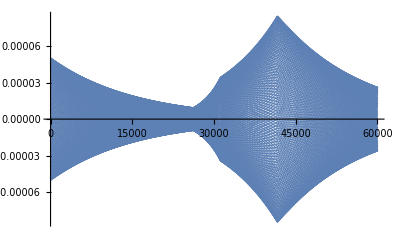

```mathematica
hWED =Table[ 0.5 m (wsol'[t])^2 + 0.5 k wsol[t],{t,0,tf,0.5}];
ListPlot[hWED]
```

## The difference in the total energies of the FPUT wave and the wave energy device is computed and plotted

```mathematica
diffE=Table[Sum[0.5(
(nsol[[j]][tt])^2+(nsol[[j]]'[tt]-nsol[[j-1]]'[tt])^2 
)+ (α/3)(nsol[[j]]'[tt]-nsol[[j-1]]'[tt])^3 ,{j,n}]-( .5 m (wsol'[tt])^2 + 0.5 k wsol[tt]),{tt,0,tf,40}]//Flatten;
```

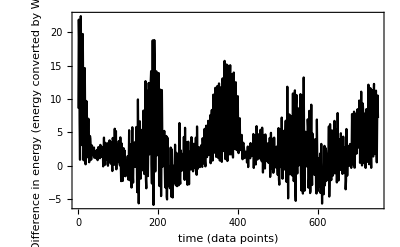

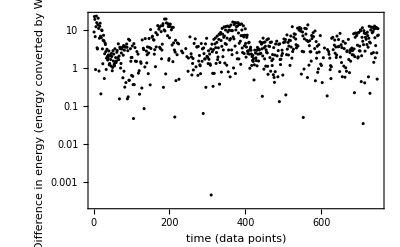

```mathematica
ListLinePlot[diffE,PlotRange->All,Frame->True,PlotStyle->{Black},FrameStyle->Black,FrameLabel->{"time (data points)","Difference in energy \n (energy converted by W.E.D)"},BaseStyle->{FontSize->12}]

ListLogPlot[diffE,PlotRange->All,Frame->True,PlotStyle->{Black},FrameStyle->Black,FrameLabel->{"time (data points)","Difference in energy \n (energy converted by W.E.D)"},BaseStyle->{FontSize->12}]
```

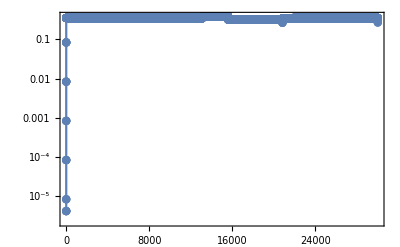

```mathematica
StepDataPlot[wsol]
```

#### Recurrence quantification

```mathematica
rm=UnitStep[0.5-DistanceMatrix[diffE]];
diffESmall=Take[diffE,400];
rmSmall=UnitStep[0.5-DistanceMatrix[diffESmall]];
diffESmall2=2Take[diffE,{90,250}];
rmSmall2=UnitStep[1-DistanceMatrix[diffESmall2]];
```

-Graphics-

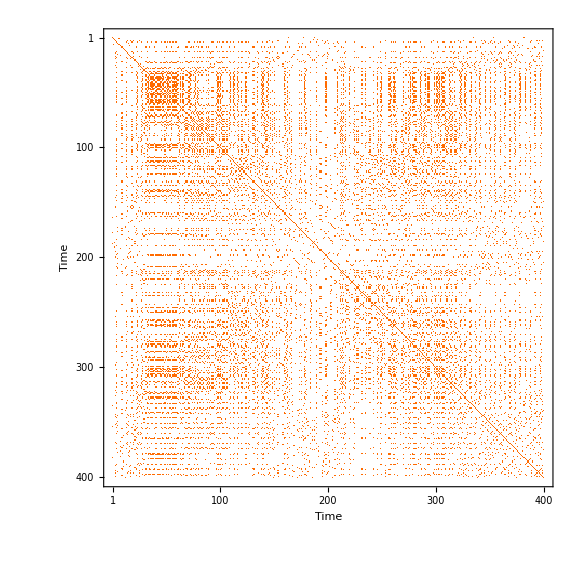

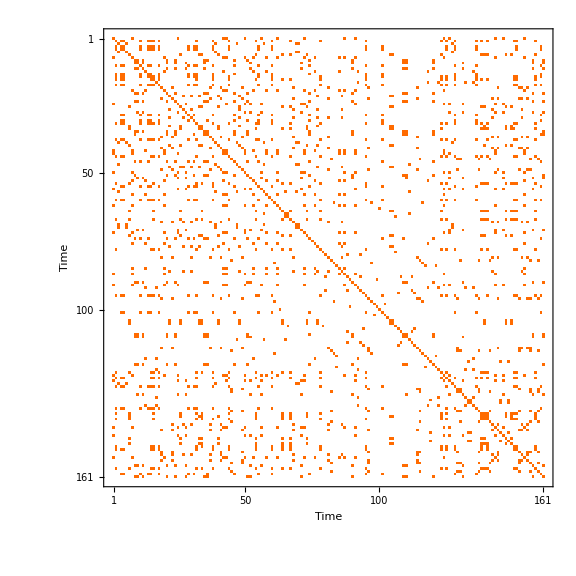

{8.59425,7.76783,21.9333,0.705032,19.9879,10.6251,5.92593,22.2697,1.14712,18.1929}

```mathematica
MatrixPlot[rm,Frame->True, FrameLabel->{"Time","Time"},FrameStyle->Directive[Black],BaseStyle->{FontSize->14}]
MatrixPlot[rmSmall,Frame->True, FrameLabel->{"Time","Time"},FrameStyle->Directive[Black],BaseStyle->{FontSize->14}]
MatrixPlot[rmSmall2,Frame->True, FrameLabel->{"Time","Time"},FrameStyle->Directive[Black],BaseStyle->{FontSize->14}]
```